```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/Ganesh

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
```

ℏ^2/(2  μ) = 20.7369

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1)^l z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
LECsNUCL=Import["../LECs_nucl_Joki.dat","Table"][[2;;]];

activeLEC=LECsNUCL[[All,{1,2,3}]];
```

In this version, I used 
x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)

```mathematica
NormTF[core_?ArrayQ]:=Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]]core[[k]][[1]]core[[l]][[1]] (Pi^2/(4 (core[[i]][[2]]+core[[j]][[2]])(core[[k]][[2]]+core[[l]][[2]])))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_,Gg_,Hh_]:=Block[{eta2,eta3,w2,w3},
eta2= (8/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(4((1/4)lam^2 Bb + Aa((1/4)lam^2 + 2Gg +2  Bb) + (1/4)lam^2Hh +2 Bb Hh+Gg((1/4)lam^2 +2Hh))^(3/2));
w2= 2(1/4)lam^2(Aa+Hh)(Gg+Bb)/((1/4)lam^2 Bb + Aa((1/4)lam^2+2 Gg+2Bb)+(1/4)lam^2 Hh +2 Bb Hh+Gg((1/4)lam^2+2Hh));
eta3 =(8/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(4((1/4)lam^2 Bb + Gg((1/4)lam^2 + 2Bb)+(1/4)lam^2Hh +2Bb Hh + Aa((1/4)lam^2+2Gg+2Hh))^(3/2));
w3 = 2(1/4)lam^2(Aa+Bb)(Gg+Hh)/((1/4)lam^2 Bb + Gg((1/4)lam^2+2Bb)+(1/4)lam^2 Hh +2Bb Hh+Aa((1/4)lam^2+2Gg+2Hh));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
];

WnolocTF3[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Gg_,Hh_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5/(2(Aa+Bb+Gg+ Hh))^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(2(2(1/4)lam^2+Aa +Bb+ Gg+Hh))^(3/2);
zeta3=-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5 Cc/(2(2(1/4)lam^2+Aa +Bb+ Gg+Hh))^(3/2);

a2=(4Hh(2(1/4)lam^2+Bb)+Gg(2(1/4)lam^2 +Bb+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b2=(Gg(4 (1./4) lam^2+2 Bb-2 Hh)+Aa (-4 (1/4) lam^2-2 Bb+2 Hh))/(2 (2 (1/4) lam^2+Aa+Bb+Gg+Hh));
c2=( Gg(2(1/4)lam^2+Bb+Hh)+Aa(2(1/4)lam^2+4Gg+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

a3= (4Bb(2(1/4)lam^2+Hh)+Gg(Bb+2(1/4)lam^2+Hh)+Aa(2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4(1/4)lam^2-2Hh)+Aa(4(1/4)lam^2+2Hh-2Bb))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2(1/4)lam^2+Hh)+Aa(4Gg+2(1/4)lam^2+Bb+Hh))/(2(2 (1/4)lam^2+Aa+Bb+Gg+Hh));

zeta1 Exp[-a1 r^2-c1 rp^2] ((+4 a1^2 r^2+b1^2 rp^2-2 a1+TwoMyOverHBsq Ee) BesselI[0.5,b1 r rp] (8 π^3 r^3 rp^3/(If[b1==0.,111,b1]))^0.5-a1 BesselI[1.5,b1 r rp] (128 π^3 r^5 rp^5 b1/3)^0.5)-zeta2 Exp[-a2 r^2-c2 rp^2] BesselI[0.5,b2 r rp] (8 π^3 r^3 rp^3/(If[b2==0.,1,b2]))^0.5-zeta3 Exp[-a3 r^2-c3 rp^2] BesselI[0.5,b3 r rp] (8 π^3 r^3 rp^3/(If[b3==0.,1,b3]))^0.5
];
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
t1=AbsoluteTime[];
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

(*Wmat=ConstantArray[0,{Npoints,Npoints}];*)

Wmats={};
SetSharedVariable[Wmats];

Do[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

wmat=ParallelTable[-hDif^3 TwoMyOverHBsq WnolocTF3[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints},ProgressReporting->False]; 

AppendTo[Wmats,cij (amat+wmat)];

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
t2=AbsoluteTime[];
Print["finite-difference runtime Δt = ",(t2-t1)/60.," mins"];
tanDelta
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,energ_:0.001]:=Module[{locall=l},
LECd=0.0;
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
-Re[TanDelSwave]/Sqrt[mh2 energ ]
]
```

EFT parameters | Numerical parameters | plot control
cutoff regulator λ = 10 | R_max = 6 | #(plot grid points) = 50
C_0(λ) = -2929.17 | #(Integration grid points) = 10 | plot threshold =  1.
B(2) = -1.77217 | dimer-basis dimension = 4 |

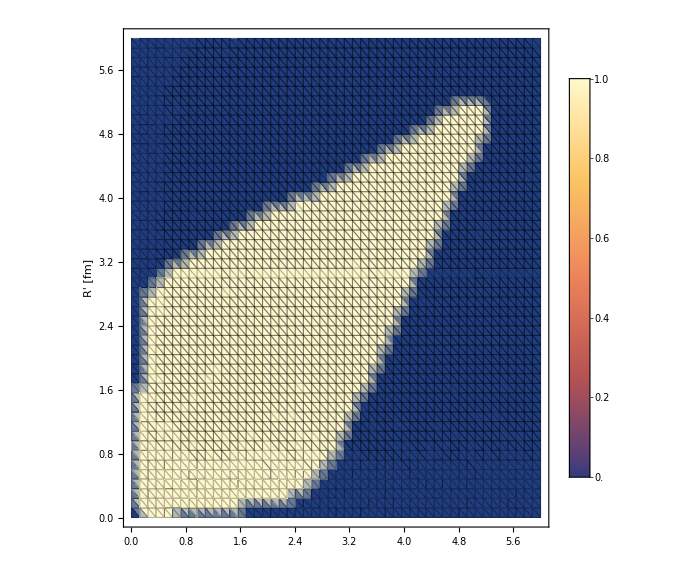
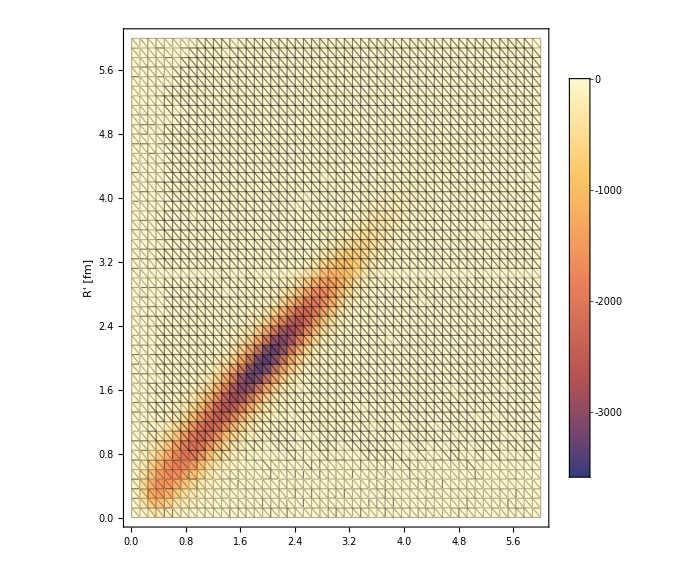
-Graphics- | -Graphics-

```mathematica
lamd=10;
rMa=6;
nGrd=10;
energ=0.001;
nR=50;
rMi=0.01;
thresh=10^-0;

dimerCore=Get["tmp.lst"];
e0Core=Get["E0tmp.lst"];
normCore=1/NormTF[dimerCore];
dimCore=Length[dimerCore];
LECc =Flatten[Select[activeLEC,#[[1]]==lamd&]][[2]];
Grid[{{"EFT parameters","Numerical parameters","plot control"},{"cutoff regulator λ = "<>ToString[lamd],"R_max = "<>ToString[rMa],"#(plot grid points) = "<>ToString[nR]},{"C_0(λ) = "<>ToString[LECc],"#(Integration grid points) = "<>ToString[nGrd],"plot threshold = "NumberForm[N[thresh]]},{"B(2) = "<>ToString[e0Core],"dimer-basis dimension = "<>ToString[dimCore]}},Frame->All]

(*tmp=GetEREP3[lamd,rMa,nGrd,dimerCore,LECc,energ];
Grid[{{"Results"},{"a_dd = "<>ToString[tmp],"a_dd/a = "<>ToString[tmp/(hbar/√(Mm Abs[e0Core]))]}},Frame->All]*)

rR=Range[rMi,rMa,(rMa-rMi)/nR];
nR=Length[rR];
potnoloc3d={};
Do[
cij=dimerCore[[ii]][[1]] dimerCore[[jj]][[1]] dimerCore[[kk]][[1]]  dimerCore[[ll]][[1]]  normCore;
potnoloc3dtmp=
Flatten[ParallelTable[{rR[[i]],rR[[j]],mh2 cij WnolocTF3[rR[[i]],rR[[j]],energ,lamd,LECc,0.0,dimerCore[[ii]][[2]],dimerCore[[jj]][[2]],dimerCore[[kk]][[2]],dimerCore[[ll]][[2]],0,mh2]}
,{i,Length[rR]},{j,Length[rR]}],1];
AppendTo[potnoloc3d,potnoloc3dtmp]
,{ii,1,dimCore},{jj,1,dimCore},{kk,1,dimCore},{ll,1,dimCore}]
potnonloc3d=Transpose[{potnoloc3d[[1]][[All,1]],potnoloc3d[[1]][[All,2]],Total[potnoloc3d[[All,All,3]]]}];
chopedMat=ParallelTable[
If[Abs[Re[potnonloc3d[[i]][[3]]]]>=thresh,{potnonloc3d[[i]][[1]],potnonloc3d[[i]][[2]],1},{potnonloc3d[[i]][[1]],potnonloc3d[[i]][[2]],0}]
,{i,Length[potnonloc3d]}];
Grid[{{
ListDensityPlot[chopedMat,Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"R' [fm]",None},{None,"R [fm]"}},FrameTicks->All]
,
ListDensityPlot[Re[potnonloc3d],Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"R' [fm]",None},{None,"R [fm]"}},FrameTicks->All]
}}]
Put[potnonloc3d,"nonlocPot_"<>ToString[lamd]<>".dat"];
```

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

finite-difference runtime Δt = 0.331533 mins

λ = 10   C_0(λ) = -2929.17     R_max = 5.     #(grid points) = 50                a_dd = 5.60535 fm        a_dd/a_aa = 1.15869

finite-difference runtime Δt = 0.46924 mins

λ = 10   C_0(λ) = -2929.17     R_max = 6.     #(grid points) = 60                a_dd = 5.51242 fm        a_dd/a_aa = 1.13948

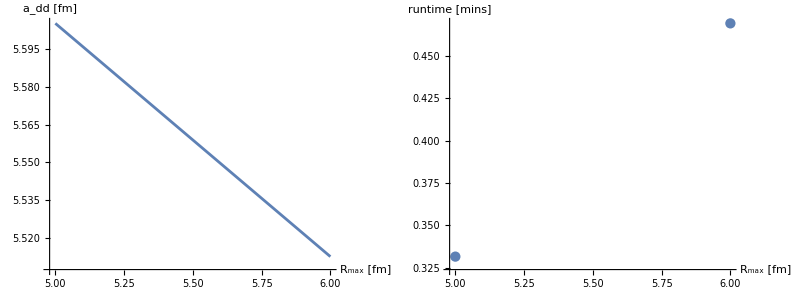

```mathematica
rMaxStart=5;
rMaxEnd=6;
nbrR=1;
RmaxRange=Range[rMaxStart,rMaxEnd,N[(rMaxEnd-rMaxStart)/nbrR]];

grdPerFermi=10;
results={};
runtimes={};
(*SetSharedVariable[results,resultsPhases];*)
Do[
nGrd=IntegerPart[rMa grdPerFermi];
ta=AbsoluteTime[];
tmp=GetEREP3[lamd,rMa,nGrd,dimerCore,LECc,energ];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["λ = ",lamd,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbar/√(Mm Abs[e0Core])),Red,18]];
,{rMa,RmaxRange}]

Grid[{{ListPlot[Transpose[{RmaxRange,results}],ImageSize->Large,Joined->True,AxesLabel->{"R_max [fm]","a_dd [fm]"}],ListPlot[runtimes,ImageSize->Large,AxesLabel->{"R_max [fm]","runtime [mins]"}]}}]
```

```mathematica
lamds={4,6,8,10};
data=Get["nonlocPot_"<>ToString[#]<>".dat"]&/@lamds;
Manipulate[ListPlot3D[Re[data[[n]]],PlotRange->All],{n,Range[1,Length[lamds],1]}]
```

### Grid - density dependence of the a_dd scattering-length pre/post-diction

```mathematica
nGrdi=3;
nGrdiMi=15;
nGrdiMa=252+nGrdiMi;
nGr=Range[nGrdiMi,nGrdiMa,Quotient[nGrdiMa-nGrdiMi,nGrdi]];

results={};
runtimes={};
(*SetSharedVariable[results,resultsPhases];*)
Do[
Print["λ = ",lamd,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd];
ta=AbsoluteTime[];
tmp=GetEREP3[lamd,rMa,nGrd,dimerCore,LECc,energ];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[runtimes,{nGrd,tb-ta}];
Print["a_dd = ",tmp," fm"];
,{nGrd,nGr}]

Grid[{{ListPlot[Transpose[{nGr,results}],ImageSize->Large,Joined->True,AxesLabel->{"#(grid points)","a_dd [fm]"}],ListPlot[Transpose[{nGr,tt}],ImageSize->Large,AxesLabel->{"#(grid points)","runtime [s]"}]}}]
```

λ = 6   C_0(λ) = -1090.55     R_max = 8     #(grid points) = 15

finite-difference runtime Δt = 0.197998 mins

a_dd = 4.96257 fm

λ = 6   C_0(λ) = -1090.55     R_max = 8     #(grid points) = 99

finite-difference runtime Δt = 1.97576 mins

a_dd = 4.95642 fm

λ = 6   C_0(λ) = -1090.55     R_max = 8     #(grid points) = 183

finite-difference runtime Δt = 6.465 mins

a_dd = 5.05838 fm

λ = 6   C_0(λ) = -1090.55     R_max = 8     #(grid points) = 267

```mathematica
results
aasy=results[[-1]]
Print["a_dd/a =",aasy/(hbar/√(Mm Abs[e0Core]))]
```

{3.92438,3.2987,5.27317,4.55745,4.26782,4.2665,4.40619,4.53118,4.61594,4.6741,4.71599}

4.71599

a_dd/a =0.878303